# Analytical Methods with Wolfram Language

Based on the presentation at https://www.youtube.com/watch?v=JTz4wkD-mxU

Set up an aid to book to do analytical work on the side.

```mathematica
Integrate[x^2,{x,0,x}]
```

x^3/3

### AiryAI Simplification

This is why you key in as much as you can in fractions to find all sorts of interesting simplifications.s

Mathematica enables you to basically copy Ramanujan and explore mathematics. Always use fractions on Mathematica to automatically find closed forms.

```mathematica
?StableDistribution
```

```mathematica
?PDF
```

```mathematica
PDF[StableDistribution[3/2,1,0,1],x]
```

-(2^(1/3) ⅇ^(x^3/27) (3^(1/3) x AiryAi[x^2/(3 2^(2/3) 3^(1/3))]+3 2^(1/3) AiryAiPrime[x^2/(3 2^(2/3) 3^(1/3))]))/(3 3^(2/3))

```mathematica
?FullSimplify
```

This was a surprising empirical fact that was found when Taleb was tinkering with Mathematica.

```mathematica
FullSimplify[PDF[StableDistribution[3/2,1,0,1],x]]
```

ⅇ^(x^3/27) (3^(1/3) x AiryAi[x^2 Root[-1+324 #1^3&,1,0]]+3 2^(1/3) AiryAiPrime[x^2 Root[-1+324 #1^3&,1,0]]) Root[2+243 #1^3&,1,0]

Another typical closed form is when α = 2 for the stable distribution.

```mathematica
PDF[StableDistribution[2,1,0,1],x]
```

(ⅇ^(-x^2/4))/(2 √π)

```mathematica
?StableDistribution
```

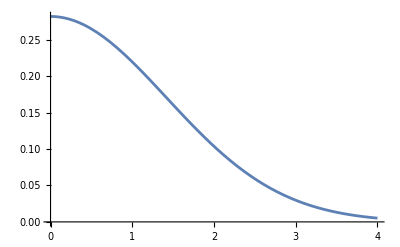

```mathematica
Plot[PDF[StableDistribution[2,1,0,1],x],{x,0,4}]
```